## Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(*Some unimportant error messages are sw
itched off for future convenience*)
Off[NIntegrate::inumr,FindRoot::lstol,NIntegrate::ncvb,ListInterpolation::inhr];
nbin=1701;
```

## Constants

```mathematica
(* The Subscript[Ω, b] h^2 value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
obh2pl=0.02236;
(* The Subscript[Ω, m] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
ompl=0.3166;
(* The Subscript[H, 0] value from Planck paper - See Table 2, page 16, 4th column of https://arxiv.org/pdf/1807.06209.pdf *)
H0pl=67.4; (*67.27*)
(* The dimensionless parameter for the Hubble constant, defined as Subscript[H, 0]/100 *)
h0pl=0.674;
dh0pl=0.005;
(* The h value from Type Ia Supernovae - See abstract of https://arxiv.org/pdf/1903.07603.pdf *)
h0riess=0.7403;
dh0riess=0.0104;
omriess=0.334;
domriess=0.02;
(* CMB temperature *)
Tcmb=2.7255;
(* Various constants useful for the following likelihoods *)
c=299792.458;
cH0=2997.92458;
```

## Equations

```mathematica
(* Define Subscript[z, equality] and Subscript[a, equality] *)
zeq[om_?NumberQ,h_?NumberQ]:=2.5*10^4 om h^2 (Tcmb/2.7)^-4;
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h]);
(* E=H/H0 for the transition model *) 
H[a_?NumberQ,om_?NumberQ,h_?NumberQ]:=100h Sqrt[a^-3 om(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))]
```

```mathematica
(*Luminosity Distance*)
Clear[DLsol,DL,dL]
DLsol[om_?NumberQ,h_?NumberQ]:=(DLsol[om,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(H[1/(1+zz),om,h]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DL[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=((c/(100h))dL[z]/.DLsol[om,h])[[1]]//Chop
```

```mathematica
(*angular diameter distance*)
DA[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=DL[z,om,h]/(1+z)^2
```

```mathematica
Dm3[z_?NumberQ,om_?NumberQ,h_?NumberQ]:=(z+1)*DA[z,om,h]
```

```mathematica
obh2=obh2pl;
ogh2=2.47*10^(-5);
```

```mathematica
R1[a_]:=(3obh2)/(4ogh2*a)
```

```mathematica
cs[a_]:=c/(Sqrt[3(R1[a]+1)])
```

```mathematica
(*transition model*)f1[a_,w0_,wa_,n_]:=(a^(-3*(1+w0+wa)))*(E^(-3*wa*HarmonicNumber[n]+3*a*n*wa*HypergeometricPFQ[{1,1,1-n},{2,2},a]))
```

```mathematica
zeq[om_?NumberQ,h_?NumberQ]:=2.5*(10^4)*om*(h^2)*((Tcmb/2.7)^(-4))
```

```mathematica
aeq[om_?NumberQ,h_?NumberQ]:=1/(1+zeq[om,h])
```

```mathematica
(*dimensionless Hubble parameter*)
```

```mathematica
e[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=Sqrt[a^(-3)*om*(1+aeq[om,h]/a)+(1-om(1+aeq[om,h]))f1[a,w0,wa,n]]
```

```mathematica
(*Sound speed*)
cs[a_?NumberQ,obh2_?NumberQ]:=c/(Sqrt[3(1+(31500 obh2(Tcmb/2.7)^-4)a)] )
```

```mathematica
(*redshift at decupling A. Theodoropoulos page 37, eq 2.42*)
g1[obh2_?NumberQ]:=(0.0783*(obh2)^(-0.238))/(1+39.5*(obh2)^(0.763));
g2[obh2_?NumberQ]:=0.560/(1+21.1*(obh2)^(1.81));
zdec[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1048(1+0.00124(obh2)^(-0.738))*(1+g1[obh2]*(om*(h^2))^(g2[obh2]));

(*comoving sound horizon*)
rs[ze_,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[x,obh2]/((x^2)*100h*e[x,om,w0,wa,n,h]),{x,0,1/(1+ze)}]
```

```mathematica
(*comoving sound horizon at decoupling*)
rsdec[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=NIntegrate[cs[a,obh2]/((a^2)*100h*e[a,om,w0,wa,n,h]),{a,0,1/(1+zdec[om,obh2,h])}]
```

```mathematica
hz[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=100h*e[1/(1+z),om,w0,wa,n,h]
```

```mathematica
(*luminosity distance*)
```

```mathematica
Clear[DLsol1,DL1,dL1]
DLsol1[om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(DLsol1[om,w0,wa,n,h]=NDSolve[{D[dL1[zz]/(1+zz),zz]==1/(h*100*e[1/(1+zz),om,w0,wa,n,h]/(100h)),dL1[0]==0},dL1,{zz,0,1300},MaxSteps->Infinity])
DL1[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c/(100h))dL1[z]/.DLsol1[om,w0,wa,n,h])[[1]]//Chop
```

```mathematica
(*angular diameter distance*)
DA1[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=DL1[z,om,w0,wa,n,h]/(1+z)^2
```

```mathematica
(*comoving angular distance at decoupling*)
Dm1[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(c/(100*h))*NIntegrate[(hz[z,om,w0,wa,n,h]/100h)^(-1),{z,0,zdec[om,obh2,h]}];
Dm2[om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(zdec[om,obh2,h]+1)*DA1[zdec[om,obh2,h],om,w0,wa,n,h];
Dm4[z_?NumberQ,om_?NumberQ,obh2_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=(z+1)*DA1[z,om,w0,wa,n,h]
```

```mathematica
Dv[z_,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=((c*z*((1+z)^2)*(DA[z,om,w0,wa,n,h]^2))/hz[z,om,w0,wa,n,h])^(1/3)
```

```mathematica
(*BAO dz ratio =rs/Dv*)
dz[z_,om_,obh2_,w0_,wa_,n_,h_]:=rs[zdec[om,obh2,h],om,obh2,w0,wa,n,h]/Dv[z,om,w0,wa,n,h]
```

```mathematica
DH[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,n_?NumberQ,h_?NumberQ]:=c/hz[z,om,w0,wa,n,h]
```

```mathematica
(*CMB shift parameter*)
R[om_,obh2_,w0_,wa_,n_,h_]:=(Sqrt[om (100h)^2]*Dm2[om,obh2,w0,wa,n,h])/c
```

```mathematica
(* Drag redshift: https://arxiv.org/pdf/astro-ph/9709112.pdf eq 4 page 5*)
zdrag[om_?NumberQ,obh2_?NumberQ,h_?NumberQ]:=1291 ((om*h^2)^0.251)/(1+0.659 (om*h^2)^0.828)(1+(0.313(om*h^2)^-0.419(1+0.607(om*h^2)^0.674))(obh2)^(0.238(om*h^2)^0.223))
```

```mathematica
la[om_,obh2_,w0_,wa_,n_,h_]:=(Pi*Dm2[om,obh2,w0,wa,n,h])/rsdec[om,obh2,w0,wa,n,h]
```

## Pantheon+ Data

```mathematica
dataPanth=Import[".\\data\\lcparam_full_long_zhel-pp.txt","Table"];
(* Length of Pantheon data *)
ndatPanth=Length[dataPanth]-1;
```

```mathematica
(* Isolate the relevant part of the Pantheon+ data: z, mb, dmb, mu=mb-M, dmu, muceph, iscamibrator(1,0) , in a short version of the Pantheon+ data. *)
tabdat=Table[{dataPanth[[1+i,3]],dataPanth[[1+i,9]],dataPanth[[1+i,10]],dataPanth[[1+i,11]],dataPanth[[1+i,12]],dataPanth[[1+i,13]],dataPanth[[1+i,14]]},{i,1,ndatPanth}];
tabdat1=Table[{dataPanth[[1+i,3]],dataPanth[[1+i,11]],dataPanth[[1+i,12]]},{i,1,ndatPanth}];
```

```mathematica
(*Assuming tabdat1 is already defined and contains 1701 data points*)(*Determine the number of data points per bin for the first nbin bins*)
numDataPoints=Length[tabdat1];
binSize=Floor[numDataPoints/nbin];(*Use Floor instead of Ceiling to have nbin equal bins*)
```

```mathematica
(*Sort the data by redshift*)
sortedData=SortBy[tabdat1,First];
```

```mathematica
(*Function to calculate the mean z,weighted mean of μ and uncertainty dμ for each bin*)
meanFunction[bin_]:=Module[{zs,mus,dmus},zs=bin[[All,1]];
mus=bin[[All,2]];
dmus=bin[[All,3]];
(*Weighted mean of μ*)weightedMean=Total[mus/dmus^2]/Total[1/dmus^2];
(*Combined uncertainty of μ*)combinedUncertainty=Sqrt[1/Total[1/dmus^2]];
(*Mean redshift*)meanZ=Mean[zs];
{meanZ,weightedMean,combinedUncertainty}]
```

```mathematica
(*Bin the data and calculate the mean for each bin containing n=binSize elements*)
tabdatbinned=Table[meanFunction[sortedData[[((i-1)*binSize+1);;(i*binSize)]]],{i,1,nbin-1}];
(*The last bin gets the remaining data points*)
lastBin=sortedData[[((nbin-1)*binSize+1);;]];
lastBinMean=meanFunction[lastBin];
tabdatbinned=Append[tabdatbinned,lastBinMean];
```

```mathematica
(*meanFunction was applied for groups of n=binSize elements, nbin=100 times and so we have ~100 results in one 3x100 matrix*)
```

```mathematica
(*mean z, weighted mean mu, combined uncertainty*)(*MatrixForm[tabdatbinned]*)
```

### Distance modulus

```mathematica
(*Function to calculate the distance modulus*)
distanceModulus[z_?NumericQ]:=5 Log10[DL[z,ompl,h0pl]]+25
```

```mathematica
(*Calculate the expected distance modulus for each zeff and add a new column to the binned data table*)
tabdatbinnedWithModulus=Table[Append[tabdatbinned[[i]],distanceModulus[tabdatbinned[[i,1]]]],{i,Length[tabdatbinned]}];
```

```mathematica
(*MatrixForm[tabdatbinnedWithModulus]*)
```

```mathematica
(*Assuming tabdatbinnedWithModulus is already defined and contains the data*)(*Create the new table*)newTable=Table[{tabdatbinnedWithModulus[[i,1]],(*z_eff*)tabdatbinnedWithModulus[[i,2]]-tabdatbinnedWithModulus[[i,4]],(*μ_observed-μ_LCDM*)tabdatbinnedWithModulus[[i,3]]  (*Uncertainty of μ_observed*)},{i,Length[tabdatbinnedWithModulus]}];
```

### Plot of mu_obs - mu_lcdm

```mathematica
(*Create a plot with error bars using the newTable*)errorPlotData=Table[{newTable[[i,1]],(*x value:z_eff*)Around[newTable[[i,2]],newTable[[i,3]]] (*y value with error:(μ_observed-μ_LCDM) with uncertainty*)},{i,Length[newTable]}];
```

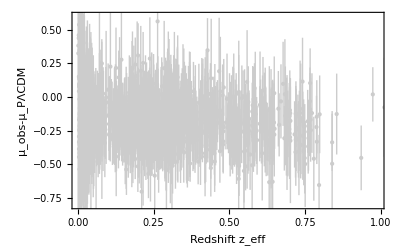

```mathematica
pl1=ListPlot[errorPlotData,PlotRange->{-0.8,0.6},Frame->True,FrameLabel->{"Redshift z_eff","μ_obs-μ_PΛCDM"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->GrayLevel[0.8]|>,PlotStyle->{GrayLevel[0.8],PointSize[Medium]},AxesOrigin->{Automatic,Automatic},Ticks->{Automatic,Automatic}]
```

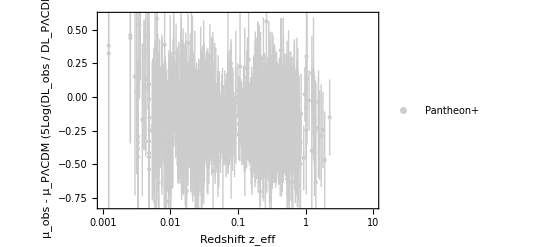

```mathematica
pl1log=ListPlot[errorPlotData,PlotRange->{{0.001,10},{-0.8,0.6}},Frame->True,FrameLabel->{"Redshift z_eff","μ_obs - μ_PΛCDM (5Log(DL_obs / DL_PΛCDM))"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->GrayLevel[0.80]|>,PlotStyle->{GrayLevel[0.80],PointSize[Medium]},PlotLegends->Placed[{"Pantheon+"},{0.85,0.95}],AxesOrigin->{Automatic,Automatic},Ticks->{Automatic,Automatic},ScalingFunctions->{"Log",None}]
```

## Binned Data (with covariance)

```mathematica
(*the full data can be found at https://github.com/PantheonPlusSH0ES/DataRelease/tree/main/Pantheon%2B_Data/4_DISTANCES_AND_COVAR and was used in https://arxiv.org/abs/2301.01024*)
dataP=Import[".\\data\\Pantheon+SH0ES.txt","Table"];
(*length of the Pantheon+ data*)
ndatP=Length[dataP]-1;
(*statistical and systematic errors*)
Dij0=Import[".\\data\\Pantheon+SH0ES_STAT+SYS.cov","List"];
Dij=Partition[Dij0[[2;;-1]],{Dij0[[1]]}];
(*Partition: Takes the elements from the second to the last of list Dij0 (thus [[2;;-1]]) and partitions them into sublists, each having a length of 1701 (thus {Dij0[[1]]}=1701)*)
Covstat=DiagonalMatrix[dataP[[All,10]][[2;;-1]]^2];
Cov=Dij;
```

```mathematica
InvCov=Inverse[Cov];
```

```mathematica
(* Isolate the relevant part of the Pantheon+ data: z, mb, dmb, mu=mb-M, dmu, muceph, iscamibrator(1,0) , in a short version of the Pantheon+ data. *)
tabdat=Table[{dataP[[1+i,3]],dataP[[1+i,9]],dataP[[1+i,10]],dataP[[1+i,11]],dataP[[1+i,12]],dataP[[1+i,13]],dataP[[1+i,14]]},{i,1,ndatP}];
tabdat1=Table[{dataP[[1+i,3]],dataP[[1+i,11]],dataP[[1+i,12]]},{i,1,ndatP}];
```

```mathematica
tabMu=Table[{tabdat[[i,1]],tabdat[[i,4]]},{i,1,Length[tabdat]}];
```

```mathematica
mu=Table[{0,mu1},Length[tabMu]];
```

```mathematica
dmu=Table[{0,dmu1},Length[tabMu]];
```

```mathematica
tabMu1=tabMu-mu;
```

```mathematica
tabMu2=Table[{tabdat[[i,1]],tabdat[[i,4]]-5*Log10[DL[tabdat[[i,1]],ompl,h0pl]]-25},{i,1,Length[tabdat]}]-dmu;
```

### Data bins

```mathematica
bin1=Table[If[tabMu[[i,1]]<0.005,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin1,_-dmu1]
```

29

```mathematica
bin1l=Table[If[0.005<tabMu[[i,1]]<0.01,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin1l,_-dmu1]
```

82

```mathematica
bin2=Table[If[0.01<tabMu[[i,1]]<0.02,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin2,_-dmu1]
```

154

```mathematica
bin2l=Table[If[0.02<tabMu[[i,1]]<0.04,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin2l,_-dmu1]
```

325

```mathematica
bin2m=Table[If[0.04<tabMu[[i,1]]<0.06,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin2m,_-dmu1]
```

88

```mathematica
bin2n=Table[If[0.06<tabMu[[i,1]]<0.08,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin2n,_-dmu1]
```

49

```mathematica
bin3=Table[If[0.08<tabMu[[i,1]]<0.1,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin3,_-dmu1]
```

14

```mathematica
bin4=Table[If[0.1<tabMu[[i,1]]<0.2,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin4,_-dmu1]
```

207

```mathematica
bin5=Table[If[0.2<tabMu[[i,1]]<0.3,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin5,_-dmu1]
```

259

```mathematica
bin6=Table[If[0.3<tabMu[[i,1]]<0.4,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin6,_-dmu1]
```

186

```mathematica
bin7=Table[If[0.4<tabMu[[i,1]]<0.6,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin7,_-dmu1]
```

179

```mathematica
bin8=Table[If[0.6<tabMu[[i,1]]<1,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin8,_-dmu1]
```

104

```mathematica
bin26=Table[If[1<tabMu[[i,1]],tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin26,_-dmu1]
```

25

```mathematica
(*stop here*)
```

```mathematica
bin26l=Table[If[1.025<tabMu[[i,1]]<1.2,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin26l,_-mu1]
```

3

```mathematica
bin27=Table[If[1.2<tabMu[[i,1]]<1.3,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin27,_-mu1]
```

3

```mathematica
bin27l=Table[If[1.3<tabMu[[i,1]]<1.35,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin27l,_-mu1]
```

5

```mathematica
bin27m=Table[If[1.35<tabMu[[i,1]]<1.40,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin27m,_-mu1]
```

3

```mathematica
bin28=Table[If[1.4<tabMu[[i,1]]<1.6,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
```

```mathematica
Count[bin28,_-mu1]
```

3

```mathematica
bin29=Table[If[1.6<tabMu[[i,1]]<2.5,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin29,_-mu1]
```

5

```mathematica
bin30=Table[If[0.8<tabMu[[i,1]]<2.5,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin30,_-dmu1]
```

30

```mathematica
bin31=Table[If[0.1<tabMu[[i,1]]<0.8,tabMu2[[i,2]],0],{i,1,Length[tabMu]}];
Count[bin31,_-dmu1]
```

930

```mathematica
bintest=Table[If[tabMu[[i,1]]<0.1,tabMu1[[i,2]],0],{i,1,Length[tabMu]}];
Count[bintest,_-mu1]
```

741

### X^2

```mathematica
(*Minimizing X^2 to obtain the distance modulus for each bin*)
```

```mathematica
x1[dmu1_]:=bin1.InvCov.(Transpose[bin1])

min1=FindMinimum[x1[dmu1],{dmu1}];
Mu1=min1[[2,1,2]]
```

0.179086

```mathematica
x1l[dmu1_]:=bin1l.InvCov.(Transpose[bin1l])

min1l=FindMinimum[x1l[dmu1],{dmu1}];
Mu1l=min1l[[2,1,2]];


x2[dmu1_]:=bin2.InvCov.(Transpose[bin2])

min2=FindMinimum[x2[dmu1],{dmu1}];
Mu2=min2[[2,1,2]];

x2l[dmu1_]:=bin2l.InvCov.(Transpose[bin2l])

min2l=FindMinimum[x2l[dmu1],{dmu1}];
Mu2l=min2l[[2,1,2]];

x2m[dmu1_]:=bin2m.InvCov.(Transpose[bin2m])

min2m=FindMinimum[x2m[dmu1],{dmu1}];
Mu2m=min2m[[2,1,2]];

x2n[dmu1_]:=bin2n.InvCov.(Transpose[bin2n])

min2n=FindMinimum[x2n[dmu1],{dmu1}];
Mu2n=min2n[[2,1,2]];

x3[dmu1_]:=bin3.InvCov.(Transpose[bin3])

min3=FindMinimum[x3[dmu1],{dmu1}];
Mu3=min3[[2,1,2]];
```

```mathematica
x4[dmu1_]:=bin4.InvCov.bin4
min4=FindMinimum[x4[dmu1],{dmu1}];
Mu4=min4[[2,1,2]];

x5[dmu1_]:=bin5.InvCov.bin5
min5=FindMinimum[x5[dmu1],{dmu1}];
Mu5=min5[[2,1,2]];
```

```mathematica
x6[dmu1_]:=bin6.InvCov.(Transpose[bin6])
min6=FindMinimum[x6[dmu1],{dmu1}];
Mu6=min6[[2,1,2]];

x7[dmu1_]:=bin7.InvCov.(Transpose[bin7])
min7=FindMinimum[x7[dmu1],{dmu1}];
Mu7=min7[[2,1,2]];

x8[dmu1_]:=bin8.InvCov.(Transpose[bin8])
min8=FindMinimum[x8[dmu1],{dmu1}];
Mu8=min8[[2,1,2]];



x26[dmu1_]:=bin26.InvCov.(Transpose[bin26])
min26=FindMinimum[x26[dmu1],{dmu1}];
Mu26=min26[[2,1,2]];
```

```mathematica
x30[dmu1_]:=(Transpose[bin30]).InvCov.bin30
min30=FindMinimum[x30[dmu1],{dmu1,0.2}];
dMu30=min30[[2,1,2]]
```

-0.133622

```mathematica
x31[dmu1_]:=bin31.InvCov.(Transpose[bin31])
min31=FindMinimum[x31[dmu1],{dmu1,45}];
dMu31=min31[[2,1,2]]
```

-0.191819

### Mu residual

```mathematica
MuMatrix={Mu1,Mu1l,Mu2,Mu2l,Mu2m,Mu2n,Mu3,Mu4,Mu5,Mu6,Mu7,Mu8,Mu26}
```

{0.179086,-0.155983,-0.144628,-0.176171,-0.188594,-0.182981,-0.156173,-0.186951,-0.193871,-0.177327,-0.200382,-0.220811,-0.100435}

```mathematica
dMuMatrix30={dMu31,dMu30};
```

```mathematica
Length[dataP]
```

1702

```mathematica
ZMatrix={Mean[tabMu[[1;;29,1]]],Mean[tabMu[[29;;111,1]]],Mean[tabMu[[111;;265,1]]],Mean[tabMu[[265;;590,1]]],Mean[tabMu[[590;;678,1]]],Mean[tabMu[[678;;727,1]]],Mean[tabMu[[727;;741,1]]],Mean[tabMu[[741;;948,1]]],Mean[tabMu[[948;;1207,1]]],Mean[tabMu[[1207;;1393,1]]],Mean[tabMu[[1393;;1572,1]]],Mean[tabMu[[1572;;1676,1]]],Mean[tabMu[[1676;;1701,1]]](*,Mean[tabMu[[1679;;1682,1]]],Mean[tabMu[[1682;;1685,1]]],Mean[tabMu[[1685;;1690,1]]],Mean[tabMu[[1693;;1693,1]]],Mean[tabMu[[1693;;1696,1]]],Mean[tabMu[[1696;;1701,1]]]*)(*,Mean[tabMu[[1676;;1697,1]]]*)}
```

{0.00377621,0.00759867,0.0150957,0.0281529,0.0482225,0.070313,0.0867567,0.157327,0.248162,0.340401,0.487974,0.700067,1.36455}

```mathematica
ZMatrix30={Mean[tabMu[[741;;1671,1]]],Mean[tabMu[[1671;;1701,1]]]};
```

```mathematica
MuZMatrix=Table[{ZMatrix[[i]],MuMatrix[[i]]},{i,1,Length[MuMatrix]}]
```

{{0.00377621,0.179086},{0.00759867,-0.155983},{0.0150957,-0.144628},{0.0281529,-0.176171},{0.0482225,-0.188594},{0.070313,-0.182981},{0.0867567,-0.156173},{0.157327,-0.186951},{0.248162,-0.193871},{0.340401,-0.177327},{0.487974,-0.200382},{0.700067,-0.220811},{1.36455,-0.100435}}

```mathematica
MuZMatrix30=Table[{ZMatrix30[[i]],dMuMatrix30[[i]]},{i,1,Length[dMuMatrix30]}]
```

{{0.339751,-0.191819},{1.28217,-0.133622}}

```mathematica
Test=Table[{MuZMatrix[[i,1]],MuZMatrix[[i,2]]},{i,1,Length[MuZMatrix]}]
```

{{0.00377621,0.179086},{0.00759867,-0.155983},{0.0150957,-0.144628},{0.0281529,-0.176171},{0.0482225,-0.188594},{0.070313,-0.182981},{0.0867567,-0.156173},{0.157327,-0.186951},{0.248162,-0.193871},{0.340401,-0.177327},{0.487974,-0.200382},{0.700067,-0.220811},{1.36455,-0.100435}}

### Errors

```mathematica
(*calculation of the 1σ error through the Fisher matrix*)
Fij1=(0.5*D[x1[dmu1],{dmu1,2}])/.dmu1->Mu1;


errors1=1/Sqrt[Fij1];
```

```mathematica
Fij1l=(0.5*D[x1l[dmu1],{dmu1,2}])/.dmu1->Mu1l;


errors1l=1/Sqrt[Fij1l];
```

```mathematica
Fij2=0.5*(D[x2[dmu1],dmu1,dmu1])/.dmu1->Mu2;


errors2=Sqrt[Fij2^(-1)]
```

0.0174062

```mathematica
Fij2l=0.5*(D[x2l[dmu1],dmu1,dmu1])/.dmu1->Mu2l;


errors2l=Sqrt[Fij2l^(-1)];
Fij2m=0.5*(D[x2m[dmu1],dmu1,dmu1])/.dmu1->Mu2m;


errors2m=Sqrt[Fij2m^(-1)];
Fij2n=0.5*(D[x2n[dmu1],dmu1,dmu1])/.dmu1->Mu2n;


errors2n=Sqrt[Fij2n^(-1)]
```

0.0192164

```mathematica
Fij3=(0.5*D[x3[dmu1],dmu1,dmu1])/.dmu1->Mu3;
errors3=Sqrt[Fij3^(-1)]
```

0.0355539

```mathematica
Fij4=(0.5*D[x4[dmu1],dmu1,dmu1])/. dmu1->Mu4;
errors4=Sqrt[Fij4^(-1)];

Fij5=0.5*(D[x5[dmu1],dmu1,dmu1])/. dmu1->Mu5;
errors5=Sqrt[Fij5^(-1)];

Fij6=(0.5*D[x6[dmu1],dmu1,dmu1])/.dmu1->Mu6;
errors6=Sqrt[Fij6^(-1)];

Fij7=(0.5*D[x7[dmu1],dmu1,dmu1])/. dmu1->Mu7;
errors7=Sqrt[Fij7^(-1)];

Fij8=(0.5*D[x8[dmu1],dmu1,dmu1])/. dmu1->Mu8;
errors8=Sqrt[Fij8^(-1)];



Fij26=0.5*(D[x26[dmu1],dmu1,dmu1])/. dmu1->Mu26;
errors26=Sqrt[Fij26^(-1)];
```

```mathematica
Fij30=0.5*(D[x30[dmu1],dmu1,dmu1])/. dmu1->dMu30;
errors30=Sqrt[Fij30^(-1)]
```

0.0462637

```mathematica
Fij31=0.5*(D[x31[dmu1],dmu1,dmu1])/.dmu1->Mu31;
errors31=Sqrt[Fij31^(-1)]
```

0.00533321

```mathematica
errors={errors1,errors1l,errors2,errors2l,errors2m,errors2n,errors3,errors4,errors5,errors6,errors7,errors8,errors26(*,errors26l,errors27,errors27l,errors27m,errors28,errors29*)(*,errorstest*)}
```

{0.0371351,0.0284105,0.0174062,0.00913251,0.0143959,0.0192164,0.0355539,0.00922989,0.00914959,0.0100113,0.0117135,0.0179589,0.0501104}

```mathematica
errorsdmu={errors31,errors30}
```

{0.00533321,0.0462637}

```mathematica
DataErrors=Table[{Test[[i,1]],Around[Test[[i,2]],errors[[i]]]},{i,1,Length[Test]}]
```

{{0.00377621,0.180.04},{0.00759867,-0.1560.028},{0.0150957,-0.1450.017},{0.0281529,-0.1760.009},{0.0482225,-0.1890.014},{0.070313,-0.1830.019},{0.0867567,-0.160.04},{0.157327,-0.1870.009},{0.248162,-0.1940.009},{0.340401,-0.1770.010},{0.487974,-0.2000.012},{0.700067,-0.2210.018},{1.36455,-0.100.05}}

```mathematica
DataErrorsdmu={{Around[MuZMatrix30[[1,1]],{0.239,0.46}],Around[MuZMatrix30[[1,2]],errorsdmu[[1]]]},{Around[MuZMatrix30[[2,1]],{0.48,1.02}],Around[MuZMatrix30[[2,2]],errorsdmu[[2]]]}}
```

{{0.340.240.5,-0.1920.005},{1.30.51.0,-0.130.05}}

### Plots

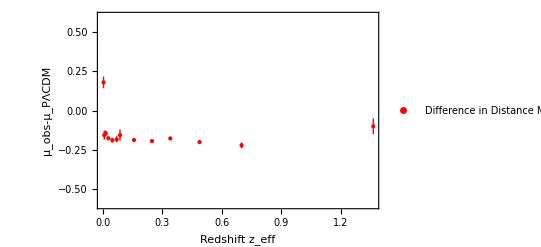

```mathematica
pl2=ListPlot[DataErrors,PlotRange->{-0.6,0.6},Frame->True,FrameLabel->{"Redshift z_eff","μ_obs-μ_PΛCDM"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Red|>,PlotStyle->{Red,PointSize[Medium]},PlotLegends->{"Difference in Distance Modulus with Uncertainties"},AxesOrigin->{Automatic,Automatic},Ticks->{Automatic,Automatic}]
```

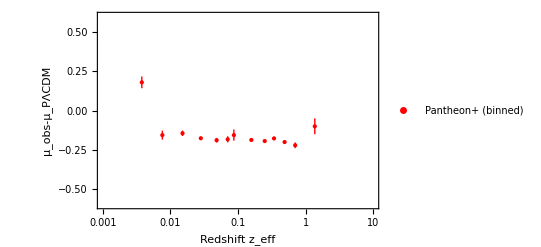

```mathematica
pl2log=ListPlot[DataErrors,PlotRange->{{0.001,10},{-0.6,0.6}},Frame->True,FrameLabel->{"Redshift z_eff","μ_obs-μ_PΛCDM"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Red|>,PlotStyle->{Red,PointSize[Medium]},PlotLegends->Placed[{"Pantheon+ (binned)"},{0.85,0.90}],AxesOrigin->{Automatic,Automatic},Ticks->{Automatic,Automatic},ScalingFunctions->{"Log",None}]
```

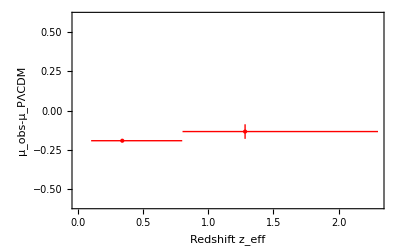

```mathematica
pldmu=ListPlot[DataErrorsdmu,PlotRange->{-0.6,0.6},Frame->True,FrameLabel->{"Redshift z_eff","μ_obs-μ_PΛCDM"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Red|>,PlotStyle->{Red,PointSize[Medium]},AxesOrigin->{Automatic,Automatic},Ticks->{Automatic,Automatic}]
```

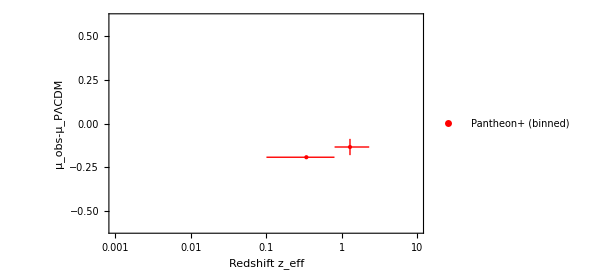

```mathematica
pldmulog=ListPlot[DataErrorsdmu,PlotRange->{{0.001,10},{-0.6,0.6}},Frame->True,FrameLabel->{"Redshift z_eff","μ_obs-μ_PΛCDM"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Red|>,PlotStyle->{Red,PointSize[Medium]},PlotLegends->Placed[{"Pantheon+ (binned)"},{0.85,0.90}],AxesOrigin->{Automatic,Automatic},Ticks->{Automatic,Automatic},ScalingFunctions->{"Log",None}]
```

## Bao Data

### Constants and Equations

```mathematica
(*Planck 2018 ΛCDM model parameters*)

H0=67.4;(*Hubble constant in km/s/Mpc*)

Ωm=0.315;(*Matter density parameter*)

ΩΛ=0.685;(*Dark energy density parameter*)

Ωr=9.26*10^-5;(*Radiation density parameter including CMB and relativistic neutrinos*)

(*Sound horizon at the drag epoch rd in Mpc,from Planck 2018*)rd=147.09;
```

```mathematica
(*Function to calculate the comoving angular diameter distance DM(z)*)
DM[z_?NumericQ]:=NIntegrate[c/(H0 Sqrt[Ωm (1+zp)^3+ΩΛ+Ωr (1+zp)^4]),{zp,0,z}]
```

### BAO data

```mathematica
(*BAO data*)(*see references at https://www.sdss4.org/science/final-bao-and-rsd-measurements/*)
baodata={(*{0.38,10.27,0.15},*){0.51,13.38,0.18},(*{0.7,17.48,0.23},*)(*{0.7,17.65,0.3},*){0.7,17.96,0.51},{0.77,18.85,0.38},(*{0.835,18.92,0.51},*){0.835,19.15,0.58}(*,{0.845,18.90,0.78}*)(*,{0.845,19.84,0.53}*),{0.85,19.5,1},{1.48,30.21,0.79},{2.33,37.6,1.9},{2.33,37.3,1.7},{0.11,2.89,0.15},{0.7,17.28,0.88},{0.87,21.38,1.39},{1.00,23.04,2.06},{2.00,36.54,1.69},{2.35,36.3,1.8},{0.38,10.20,1.17},{2.40,36.6,1.2},{0.51,13.62,0.25},{0.71,16.85,0.32},{0.93,21.71,0.28},{1.32,27.79,0.69},{2.33,39.71,0.94},{0.51,13.62,0.25},{0.71,16.85,0.32},{0.93,21.71,0.28},{1.32,27.79,0.69},{2.33,39.71,0.94}}; 
(*old data*)
baodataold={{2.34,37.68,2.17},(*{2.36,36.29,1.34},*){0.38,10.27,0.15},{0.51,13.38,0.18},{0.61,15.45,0.22},{0.81,19.46,0.78},{2.40,36.6,1.2},{0.24,6.94,0.38},{0.32,8.76,0.15},{0.44,11.79,1.11},{0.51,11.92,0.18},{0.54,14.19,0.63},{0.6,14.99,1.04},{0.73,18.03,1.26}(*,{2.34,37.68,2.17},{2.36,36.29,1.34}*)};
```

```mathematica
(*Calculate the predicted DM values for the given effective redshifts*)
DMpredictions=Table[{zeff,DM[zeff]/rd},{zeff,baodata[[All,1]]}];

(*Assuming DMpredictions and baodata are already defined in your session*)(*Extract the DM values and their errors from baodata*)
DMdataValues=baodata[[All,2]];
DMdataErrors=baodata[[All,3]];

(*Extract the predicted DM values from DMpredictions*)
DMpredictedValues=DMpredictions[[All,2]];
(*Calculate the ratio of DM data over DM predictions*)
DMratios=DMdataValues/DMpredictedValues;


(*Calculate the ratio of DM data errors over DM predictions*)
DMerrorRatios=DMdataErrors/DMpredictedValues;
(*Construct the new table with zeff,DM ratios,and DM error ratios*)
newTable=Table[{baodata[[i,1]],DMratios[[i]],DMerrorRatios[[i]]},{i,Length[baodata]}];
```

### Merging points

```mathematica
(*Retrieve the last two points with zeff=2.33 and the ones with zeff=0.7*)
pointsToMerge=Select[newTable,First[#]==2.33&];

pointsToMerge5=Select[newTable,First[#]==0.38&];
```

```mathematica
(*Calculate the weighted mean of the DM ratios*)
weights=1/pointsToMerge[[All,3]]^2;

weights5=1/pointsToMerge5[[All,3]]^2;
```

```mathematica
weightedDMRatios=Total[pointsToMerge[[All,2]]*weights]/Total[weights];

weightedDMRatios5=Total[pointsToMerge5[[All,2]]*weights5]/Total[weights5];

(*Calculate the combined uncertainty*)
combinedUncertainty=1/Sqrt[Total[weights]];

combinedUncertainty5=1/Sqrt[Total[weights5]];

(*Replace the points with the new combined points*)
newTable=DeleteCases[newTable,{2.33,_,_}];

newTable=DeleteCases[newTable,{0.38,_,_}];
newTable=Append[newTable,{2.33,weightedDMRatios,combinedUncertainty}];

newTable=Append[newTable,{0.38,weightedDMRatios5,combinedUncertainty5}];
```

```mathematica
(*Sort the new table by zeff*)
newTable=SortBy[newTable,First];
```

### Plot for the 5 log[d_Ldata/d_Lprediction]

```mathematica
(*Calculate 5*log10 of the DM ratios and propagate the uncertainties*)logDMRatiosWithErrors=Table[{newTable[[i,1]],Around[5*Log10[newTable[[i,2]]],5/Log[10]*newTable[[i,3]]/newTable[[i,2]]]},{i,Length[newTable]}];
```

```mathematica
MatrixForm[logDMRatiosWithErrors]
```

(0.11 | -0.250.11
0.38 | -0.050.25
0.51 | -0.0180.029
0.51 | 0.020.04
0.51 | 0.020.04
0.7 | -0.040.11
0.7 | 0.050.06
0.71 | -0.120.04
0.71 | -0.120.04
0.77 | -0.010.04
0.835 | -0.120.07
0.85 | -0.110.11
0.87 | 0.060.14
0.93 | -0.0200.028
0.93 | -0.0200.028
1. | 0.000.19
1.32 | -0.020.05
1.32 | -0.020.05
1.48 | 0.000.06
2. | 0.030.10
2.33 | 0.0030.033
2.35 | -0.170.11
2.4 | -0.180.07)

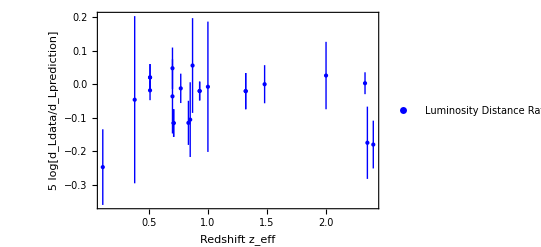

```mathematica
plBao=ListPlot[Table[{logDMRatiosWithErrors[[i,1]],logDMRatiosWithErrors[[i,2]]},{i,Length[logDMRatiosWithErrors]}],PlotRange->All,Frame->True,FrameLabel->{"Redshift z_eff","5 log[d_Ldata/d_Lprediction]"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Blue|>,PlotStyle->{Blue,PointSize[Medium]},PlotLegends->{"Luminosity Distance Ratios with Uncertainties"},AxesOrigin->{First[logDMRatiosWithErrors][[1]],Automatic},Ticks->{Automatic,Automatic}]
```

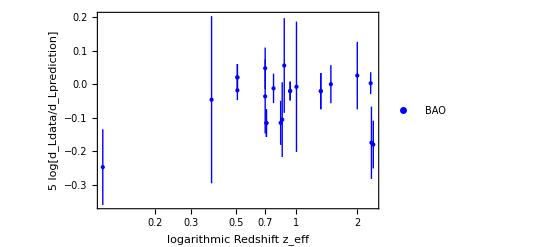

```mathematica
plBaolog=ListPlot[Table[{logDMRatiosWithErrors[[i,1]],logDMRatiosWithErrors[[i,2]]},{i,Length[logDMRatiosWithErrors]}],PlotRange->All,Frame->True,FrameLabel->{"logarithmic Redshift z_eff","5 log[d_Ldata/d_Lprediction]"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Blue|>,PlotStyle->{Blue,PointSize[Medium]},PlotLegends->Placed[{"BAO"},{0.85,0.85}],AxesOrigin->{First[logDMRatiosWithErrors][[1]],Automatic},Ticks->{Automatic,Automatic},ScalingFunctions->{"Log",None}]
```

## Old BAO data

```mathematica
(*Calculate the predicted DM values for the given effective redshifts*)
DMpredictions2=Table[{zeff,DM[zeff]/rd},{zeff,baodataold[[All,1]]}];
(*Assuming DMpredictions and baodata are already defined in your session*)(*Extract the DM values and their errors from baodata*)
DMdataValues2=baodataold[[All,2]];
DMdataErrors2=baodataold[[All,3]];

(*Extract the predicted DM values from DMpredictions*)
DMpredictedValues2=DMpredictions2[[All,2]];
(*Calculate the ratio of DM data over DM predictions*)
DMratios2=DMdataValues2/DMpredictedValues2;


(*Calculate the ratio of DM data errors over DM predictions*)
DMerrorRatios2=DMdataErrors2/DMpredictedValues2;
(*Construct the new table with zeff,DM ratios,and DM error ratios*)
newTable2=Table[{baodataold[[i,1]],DMratios2[[i]],DMerrorRatios2[[i]]},{i,Length[baodataold]}];
```

```mathematica
newTable2=SortBy[newTable2,First]
```

{{0.24,1.01574,0.0556169},{0.32,0.982304,0.0168203},{0.38,0.985674,0.0143964},{0.44,0.993419,0.093528},{0.51,0.88339,0.0133398},{0.51,0.991591,0.0133398},{0.54,1.00147,0.0444628},{0.6,0.9681,0.0671664},{0.61,0.984177,0.0140142},{0.73,0.992177,0.0693368},{0.81,0.986646,0.039547},{2.34,0.959973,0.0552851},{2.4,0.920542,0.0301817}}

### Merging points

```mathematica
pointsToMerge3old=Select[newTable2,First[#]==0.51&];
```

```mathematica
weights3old=1/pointsToMerge3old[[All,3]]^2;
```

```mathematica
weightedDMRatios3old=Total[pointsToMerge3old[[All,2]]*weights3old]/Total[weights3old];
```

```mathematica
combinedUncertainty3old=1/Sqrt[Total[weights3old]];
```

```mathematica
newTable2=DeleteCases[newTable2,{0.51,_,_}];

newTable2=Append[newTable2,{0.51,weightedDMRatios3old,combinedUncertainty3old}];
```

### Plot for the 5 log[d_Ldata/d_Lprediction] (old)

```mathematica
logDMRatiosWithErrors2=Table[{newTable2[[i,1]],Around[5*Log10[newTable2[[i,2]]],5/Log[10]*newTable2[[i,3]]/newTable2[[i,2]]]},{i,Length[newTable2]}]
```

{{0.24,0.030.12},{0.32,-0.040.04},{0.38,-0.0310.032},{0.44,-0.010.20},{0.54,0.000.10},{0.6,-0.070.15},{0.61,-0.0350.031},{0.73,-0.020.15},{0.81,-0.030.09},{2.34,-0.090.13},{2.4,-0.180.07},{0.51,-0.1400.022}}

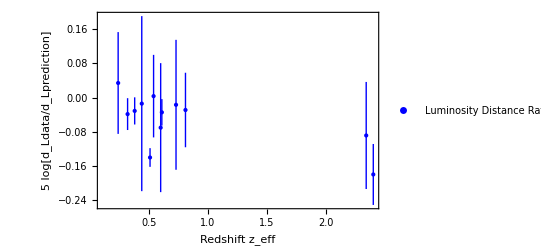

```mathematica
plBaoold=ListPlot[Table[{logDMRatiosWithErrors2[[i,1]],logDMRatiosWithErrors2[[i,2]]},{i,Length[logDMRatiosWithErrors2]}],PlotRange->All,Frame->True,FrameLabel->{"Redshift z_eff","5 log[d_Ldata/d_Lprediction]"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Blue|>,PlotStyle->{Blue,PointSize[Medium]},PlotLegends->{"Luminosity Distance Ratios with Uncertainties (old)"},AxesOrigin->{First[logDMRatiosWithErrors][[1]],Automatic},Ticks->{Automatic,Automatic}]
```

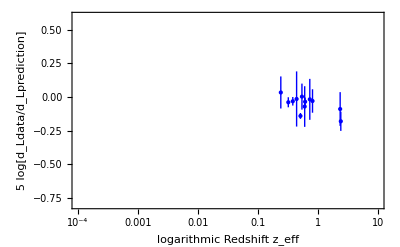

```mathematica
plBaologold=ListPlot[Table[{logDMRatiosWithErrors2[[i,1]],logDMRatiosWithErrors2[[i,2]]},{i,Length[logDMRatiosWithErrors2]}],PlotRange->{{0.0001,10},{-0.8,0.6}},Frame->True,FrameLabel->{"logarithmic Redshift z_eff","5 log[d_Ldata/d_Lprediction]"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Blue|>,PlotStyle->{Blue,PointSize[Medium]},AxesOrigin->{First[logDMRatiosWithErrors][[1]],Automatic},Ticks->{Automatic,Automatic},ScalingFunctions->{"Log",None}]
```

## WCDM and LsCDM

```mathematica
(*H for the wCDM*)
Hwcdm[z_?NumberQ,om_?NumberQ,w_?NumberQ,h_?NumberQ]:=100*h*Sqrt[((1+z)^3)*om*(1+aeq[om,h]*(z+1))+(1-om(1+aeq[om,h]))*((1+z)^(3*(1+w)))]
```

```mathematica
Hls[z_?NumberQ,om_?NumberQ,ol_?NumberQ,or_?NumberQ,h_?NumberQ,zt_?NumberQ]:=100h*Sqrt[or(1+z)^4+om(1+z)^3+ol(If[zt-z<0,-1,+1])]
```

```mathematica
(*Luminosity Distance for the wcdm*)

DLsolw[om_?NumberQ,w_?NumberQ,h_?NumberQ]:=(DLsolw[om,w,h]=NDSolve[{D[dL[zz]/(1+zz),zz]==1/(Hwcdm[zz,om,w,h]/(100h)),dL[0]==0},dL,{zz,0,1300},MaxSteps->Infinity])
DLw[z_?NumberQ,om_?NumberQ,w_?NumberQ,h_?NumberQ]:=((c/(100h))dL[z]/.DLsolw[om,w,h])[[1]]//Chop
```

```mathematica
(*Luminosity distance for the LsCDM*)
```

```mathematica
DLsols[om_?NumberQ,ol_?NumberQ,or_?NumberQ,h_?NumberQ,zt_?NumberQ]:=(DLsols[om,ol,or,h,zt]=NDSolve[{D[dLs[zz]/(1+zz),zz]==1/(Hls[zz,om,ol,or,h,zt]/(100h)),dLs[0]==0},dLs,{zz,0,1300},MaxSteps->Infinity])
DLs[z_?NumberQ,om_?NumberQ,ol_?NumberQ,or_?NumberQ,h_?NumberQ,zt_?NumberQ]:=((c/(100h))dLs[z]/.DLsols[om,ol,or,h,zt])[[1]]//Chop
```

```mathematica
(*Angular diameter distance*)
```

```mathematica
DAw[z_?NumberQ,om_?NumberQ,w_?NumberQ,h_?NumberQ]:=DLw[z,om,w,h]/(1+z)^2
```

```mathematica
DAs[z_?NumberQ,om_?NumberQ,ol_?NumberQ,or_?NumberQ,h_?NumberQ,zt_?NumberQ]:=DLs[z,om,ol,or,h,zt]/(1+z)^2
```

```mathematica
(*Comoving angular diameter distance*)
```

```mathematica
Dmw[z_?NumberQ,om_?NumberQ,w_?NumberQ,h_?NumberQ]:=(z+1)*DAw[z,om,w,h]
```

```mathematica
Dms[z_?NumberQ,om_?NumberQ,ol_?NumberQ,or_?NumberQ,h_?NumberQ,zt_?NumberQ]:=(z+1)*DAs[z,om,ol,or,h,zt]
```

```mathematica
h0riess20=0.732; (*h0 from Riess 2020*)
omModel=0.267;(*Ωm and w calculated for h0Riess using the method in https://arxiv.org/abs/2004.08363*)
wModel=-1.188;
orLs=2.469*10^(-5)*h0Ls^(-2)*(1+0.2271*3.046); (*https://arxiv.org/abs/2108.09239*)
orLspl=2.469*10^(-5)*h0pl^(-2)*(1+0.2271*3.046);
omLs=0.29;
h0Ls=0.698;
```

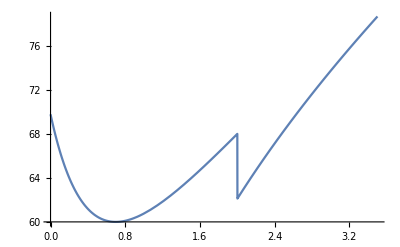

```mathematica
Plot[Hls[z,omLs,1-omLs-orLs,orLs,h0Ls,2]/(1+z),{z,0,3.5}]
```

```mathematica
(*luminosity distances for the wcdm model and the planck values*)(*model taken from https://arxiv.org/pdf/2004.08363.pdf fig 6, third line*)
DLmodel[z_]:=DLw[z,omModel,wModel,h0riess20]
DLpl[z_]:=DLw[z,ompl,-1,h0pl]
(*distance modulus (mu) for each distance*)
logDLmodel[z_]:=5*Log10[DLmodel[z]]
logDLpl[z_]:=5*Log10[DLpl[z]]
(*difference in mu*)
mudiff[z_]:=logDLmodel[z]-logDLpl[z]
```

```mathematica
(*luminosity distances for the lscdm model and the planck values*)
DLmodels[z_]:=DLs[z,omLs,1-omLs-orLs,orLs,h0Ls,2]
DLpls[z_]:=DL[z,ompl,h0pl]
(*distance modulus (mu) for each distance*)
logDLmodels[z_]:=5*Log10[DLmodels[z]]
logDLpls[z_]:=5*Log10[DLpls[z]]
(*difference in mu*)
mudiffs[z_]:=logDLmodels[z]-logDLpls[z]
```

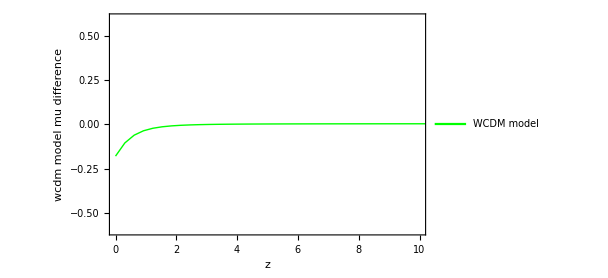

```mathematica
plwcdm=Plot[mudiff[z],{z,0,1000},ImageSize->450,Frame->True,FrameLabel->{"z","wcdm model mu difference"},PlotStyle->{Green,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,10},{-0.6,0.6}},PlotLegends->Placed[{"WCDM model"},{0.85,0.6}]]
```

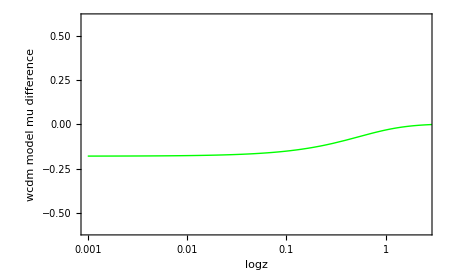

```mathematica
plwcdmlog=Plot[mudiff[z],{z,0.001,1100},ImageSize->450,Frame->True,FrameLabel->{"logz","wcdm model mu difference"},PlotStyle->{Green,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{-10,2.5},{-0.6,0.6}},ScalingFunctions->{"Log",None}]
```

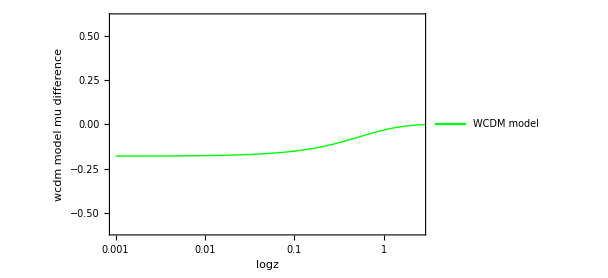

```mathematica
plwcdmLog=Plot[mudiff[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"logz","wcdm model mu difference"},PlotStyle->{Green,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{-10,2.5},{-0.6,0.6}},ScalingFunctions->{"Log",None},PlotLegends->Placed[{"WCDM model"},{0.85,0.80}]]
```

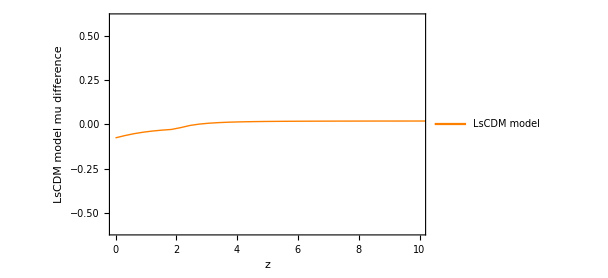

```mathematica
pls1=Plot[mudiffs[z],{z,0,1000},ImageSize->450,Frame->True,FrameLabel->{"z","LsCDM model mu difference"},PlotStyle->{Orange,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,10},{-0.6,0.6}},PlotLegends->Placed[{"LsCDM model"},{0.7,0.8}]]
```

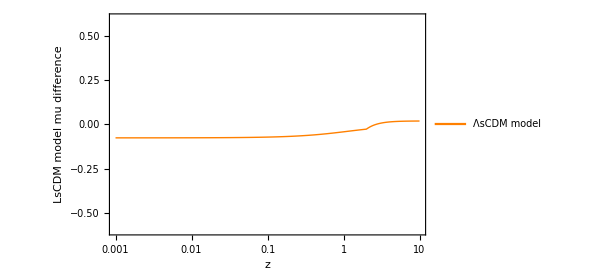

```mathematica
pls2=Plot[mudiffs[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","LsCDM model mu difference"},PlotStyle->{Orange,Thick},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,10},{-0.6,0.6}},ScalingFunctions->{"Log",None},PlotLegends->Placed[{"ΛsCDM model"},{0.85,0.75}]]
```

## CMB point and SH0ES additional points

```mathematica
(*Taken from https://arxiv.org/pdf/2102.06012.pdf *)
Mplanck=−19.401;
Mriess=-19.244;
sMplanck=0.027;
sMriess=0.037;
omPanth=0.332647;
```

```mathematica
(*Additional points to be added*)
additionalPoints={{1089,0.0,sMplanck},{0.002,Mplanck-Mriess,sMriess}}
```

{{1089,0.,0.027},{0.002,-0.157,0.037}}

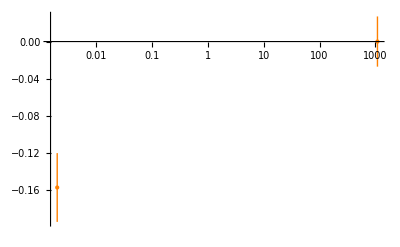

```mathematica
plcmb=ListPlot[Table[{additionalPoints[[i,1]],Around[additionalPoints[[i,2]],additionalPoints[[i,3]]]},{i,Length[additionalPoints]}],PlotRange->All,PlotStyle->{PointSize[Large],Orange},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Orange|>,ScalingFunctions->{"Log",None}]
```

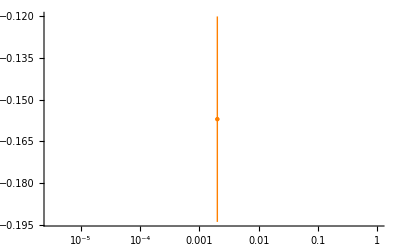

```mathematica
pLcmb=ListPlot[Table[{additionalPoints[[i,1]],Around[additionalPoints[[i,2]],additionalPoints[[i,3]]]},{i,2,2}],PlotRange->All,PlotStyle->{PointSize[Large],Orange},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Orange|>,ScalingFunctions->{"Log",None}]
```

```mathematica
(*Horizontal bands corresponding to the 1σ error*)
horizontalBand={{LightBlue,Rectangle[{-100,Mplanck-Mriess-sMriess},{1089,Mplanck-Mriess+sMriess}]},{LightGray,Rectangle[{-100,Mplanck-Mplanck-sMplanck},{1089,Mplanck-Mplanck+sMplanck}]}}
```

{{RGBColor[0.87, 0.94, 1],Rectangle[{-100,-0.194},{1089,-0.12}]},{GrayLevel[0.85],Rectangle[{-100,-0.027},{1089,0.027}]}}

```mathematica
HorizontalBand={GrayLevel[0.5700000000000001],Rectangle[{-100,-0.027},{1089,0.027}]}
```

{GrayLevel[0.5700000000000001],Rectangle[{-100,-0.027},{1089,0.027}]}

```mathematica
test[z_]:=5*Log10[DL[z,omriess,h0riess]/DL[z,ompl,h0pl]]
```

```mathematica
err1[z_]:=Sqrt[(5/Log[10]*dh0riess/(DL[z,omriess,h0riess]/DL[z,ompl,h0pl]))^2+(5/Log[10]*domriess/(DL[z,omriess,h0riess]/DL[z,ompl,h0pl]))^2]+test[z]
```

```mathematica
err2[z_]:=-Sqrt[(5/Log[10]*dh0riess/(DL[z,omriess,h0riess]/DL[z,ompl,h0pl]))^2+(5/Log[10]*domriess/(DL[z,omriess,h0riess]/DL[z,ompl,h0pl]))^2]+test[z]
```

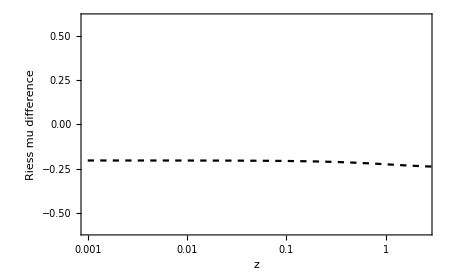

```mathematica
plRiess=Plot[test[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","Riess mu difference"},PlotStyle->{Black,Dashing[0.01]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{-1,2.5},{-0.6,0.6}},ScalingFunctions->{"Log",None}]
```

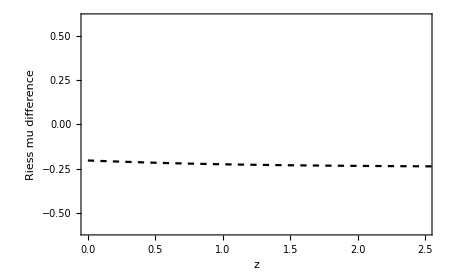

```mathematica
plRiess1=Plot[test[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","Riess mu difference"},PlotStyle->{Black,Dashing[0.01]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,2.5},{-0.6,0.6}}]
```

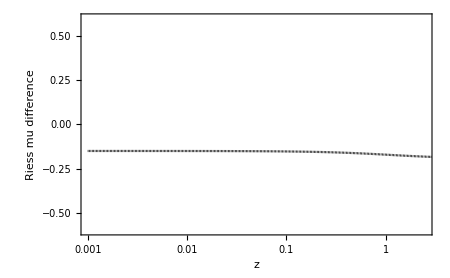

```mathematica
plerror1=Plot[err1[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","Riess mu difference"},PlotStyle->{Black,Dashing[0.001]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{-1,2.5},{-0.6,0.6}},ScalingFunctions->{"Log",None}]
```

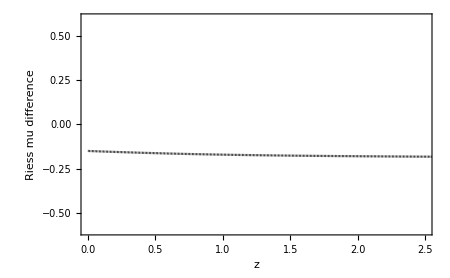

```mathematica
plerror3=Plot[err1[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","Riess mu difference"},PlotStyle->{Black,Dashing[0.001]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,2.5},{-0.6,0.6}}]
```

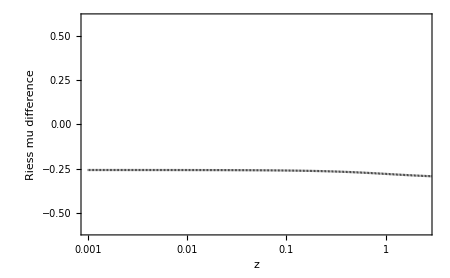

```mathematica
plerror2=Plot[err2[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","Riess mu difference"},PlotStyle->{Black,Dashing[0.001]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{-1,2.5},{-0.6,0.6}},ScalingFunctions->{"Log",None}]
```

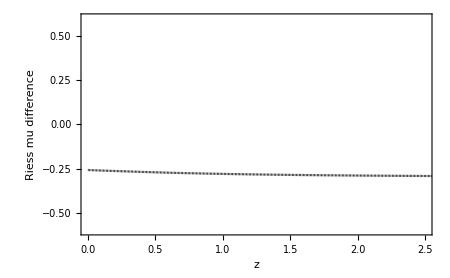

```mathematica
plerror4=Plot[err2[z],{z,0.001,10},ImageSize->450,Frame->True,FrameLabel->{"z","Riess mu difference"},PlotStyle->{Black,Dashing[0.001]},LabelStyle->Directive[Black],BaseStyle->{Large,FontFamily->"Times",18},LabelStyle->Directive[Black,Large],PlotRange->{{0,2.5},{-0.6,0.6}}]
```

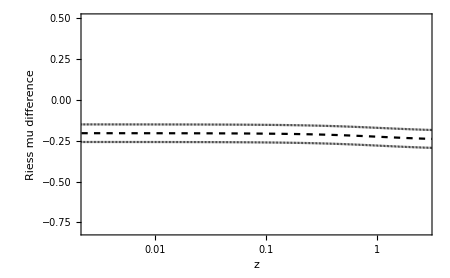

```mathematica
plRiessErr=Show[plRiess,plerror1,plerror2,PlotRange->{{-6,1},{-0.8,0.5}}]
```

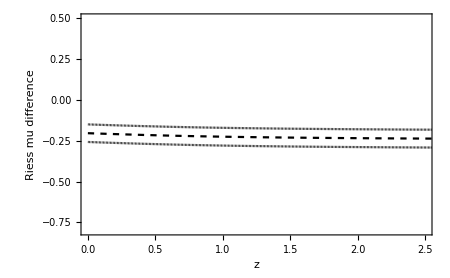

```mathematica
plRiessErr1=Show[plRiess1,plerror3,plerror4,PlotRange->{{0,2.5},{-0.8,0.5}}]
```

## Complete Plot

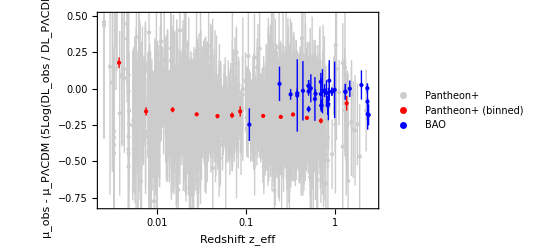

```mathematica
plfin=Show[pl1log,pl2log,plBaolog,plBaologold,PlotRange->{{-6,1},{-0.8,0.5}}]
```

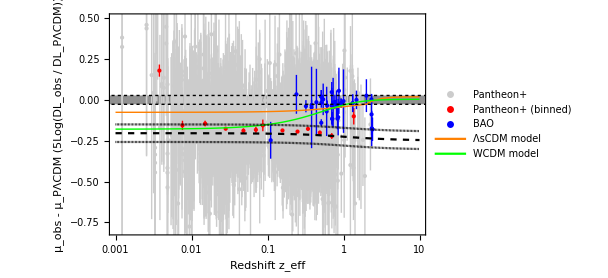

```mathematica
plfins1=Show[pl1log,pl2log,plBaolog,plBaologold,pls2,plwcdmLog,plRiessErr,Prolog->{HorizontalBand},PlotRange->{All,{-0.8,0.5}},Epilog->{{Dashing[0.005],Line[{{-30,sMplanck},{8,sMplanck}}],Line[{{-30,-sMplanck},{8,-sMplanck}}]}},ImageSize->450]
```

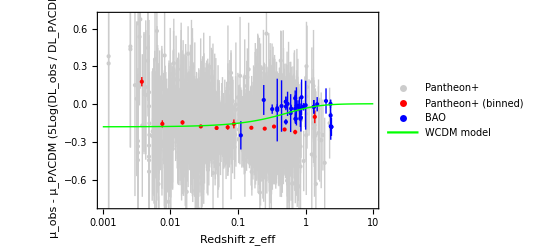

```mathematica
plfinwcdm=Show[pl1log,pl2log,plBaolog,plBaologold,plwcdmLog,PlotRange->{All,{-0.8,0.7}}]
```

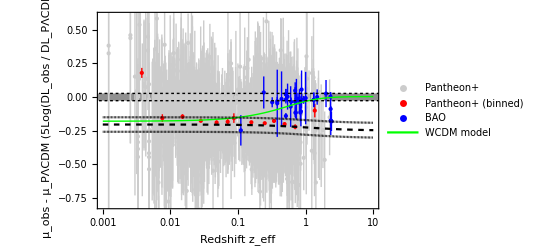

```mathematica
plFinwcdm=Show[pl1log,pl2log,plBaolog,plBaologold,plwcdmLog,plRiessErr,Prolog->{HorizontalBand},PlotRange->{All,{-0.8,0.6}},Epilog->{{Dashing[0.005],Line[{{-30,sMplanck},{8,sMplanck}}],Line[{{-30,-sMplanck},{8,-sMplanck}}]}}]
```

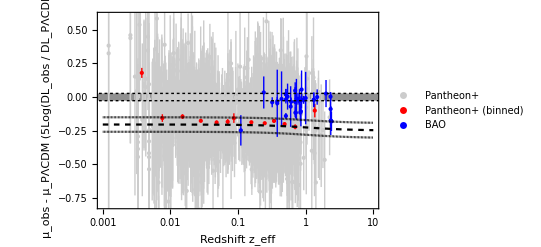

```mathematica
plFin=Show[pl1log,pl2log,plBaolog,plBaologold,plRiessErr,Prolog->{HorizontalBand},PlotRange->{All,{-0.8,0.6}},Epilog->{{Dashing[0.005],Line[{{-30,sMplanck},{8,sMplanck}}],Line[{{-30,-sMplanck},{8,-sMplanck}}]}}]
```

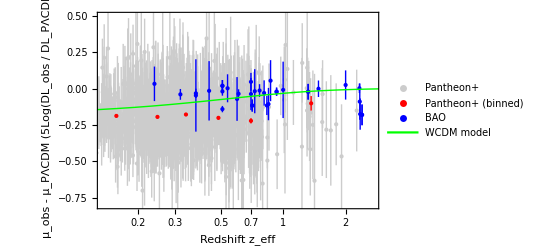

```mathematica
plfinshort=Show[pl1log,pl2log,plBaolog,plBaologold,plwcdmLog,PlotRange->{{-2,1},{-0.8,0.5}}]
```

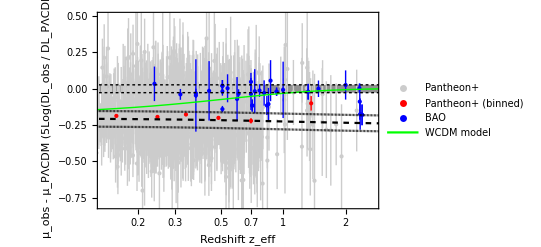

```mathematica
plfinshort2=Show[pl1log,pl2log,plBaolog,plBaologold,plwcdmLog,plRiessErr,Prolog->{HorizontalBand},PlotRange->{{-2,1},{-0.8,0.5}},Epilog->{{Dashing[0.005],Line[{{-30,sMplanck},{8,sMplanck}}],Line[{{-30,-sMplanck},{8,-sMplanck}}]}}]
```

### New bins for another plot

```mathematica
BaoBin1={{0.11,2.89,0.15},{0.24,6.94,0.38},{0.32,8.76,0.15},{0.38,10.2,1.17},{0.38,10.27,0.15},{0.44,11.79,1.11},{0.51,11.92,0.18},{0.51,13.38,0.18},{0.51,13.38,0.18},{0.51,13.62,0.25},{0.51,13.62,0.25},{0.54,14.19,0.63},{0.6,14.99,1.04},{0.61,15.45,0.22},{0.7,17.28,0.88},{0.7,17.96,0.51},{0.71,16.85,0.32},{0.71,16.85,0.32},{0.73,18.03,1.26},{0.77,18.85,0.38}};
```

```mathematica
BaoBin2={{0.81,19.46,0.78},{0.835,19.15,0.58},{0.85,19.5,1},{0.87,21.38,1.39},{0.93,21.71,0.28},{0.93,21.71,0.28},{1.,23.04,2.06},{1.32,27.79,0.69},{1.32,27.79,0.69},{1.48,30.21,0.79}};
BaoBin3={{2.,36.54,1.69},{2.33,37.3,1.7},{2.33,37.6,1.9},{2.33,39.71,0.94},{2.33,39.71,0.94},{2.34,37.68,2.17},{2.35,36.3,1.8},{2.4,36.6,1.2},{2.4,36.6,1.2}};
```

### Mu residual

```mathematica
mudiffBao1=Table[{BaoBin1[[i,1]],5*Log10[(BaoBin1[[i,2]])/(DM[BaoBin1[[i,1]]]/rd)],(5/Log[10])*((BaoBin1[[i,3]]/(DM[BaoBin1[[i,1]]]/rd))/(BaoBin1[[i,2]]/(DM[BaoBin1[[i,1]]]/rd)))},{i,1,Length[BaoBin1]}]
```

{{0.11,-0.247012,0.112706},{0.24,0.0339146,0.118899},{0.32,-0.0387696,0.0371827},{0.38,-0.0461858,0.249081},{0.38,-0.0313344,0.0317158},{0.44,-0.0143374,0.204439},{0.51,-0.269236,0.0327907},{0.51,-0.0183372,0.0292126},{0.51,-0.0183372,0.0292126},{0.51,0.0202678,0.0398582},{0.51,0.0202678,0.0398582},{0.54,0.00319235,0.0964079},{0.6,-0.0703979,0.150656},{0.61,-0.0346349,0.0309206},{0.7,-0.0362206,0.110584},{0.7,0.0475924,0.0616621},{0.71,-0.115729,0.0412386},{0.71,-0.115729,0.0412386},{0.73,-0.017054,0.15175},{0.77,-0.0123164,0.043775}}

```mathematica
mudiffBao2=Table[{BaoBin2[[i,1]],5*Log10[(BaoBin2[[i,2]])/(DM[BaoBin2[[i,1]]]/rd)],(5/Log[10])*((BaoBin2[[i,3]]/(DM[BaoBin2[[i,1]]]/rd))/(BaoBin2[[i,2]]/(DM[BaoBin2[[i,1]]]/rd)))},{i,1,Length[BaoBin2]}]
```

{{0.81,-0.0291935,0.0870374},{0.835,-0.115148,0.0657678},{0.85,-0.105543,0.111358},{0.87,0.0557192,0.141176},{0.93,-0.0202894,0.0280061},{0.93,-0.0202894,0.0280061},{1.,-0.0075989,0.194151},{1.32,-0.0205766,0.0539157},{1.32,-0.0205766,0.0539157},{1.48,-0.0000125371,0.0567846}}

```mathematica
mudiffBao3=Table[{BaoBin3[[i,1]],5*Log10[(BaoBin3[[i,2]])/(DM[BaoBin3[[i,1]]]/rd)],(5/Log[10])*((BaoBin3[[i,3]]/(DM[BaoBin3[[i,1]]]/rd))/(BaoBin3[[i,2]]/(DM[BaoBin3[[i,1]]]/rd)))},{i,1,Length[BaoBin3]}]
```

{{2.,0.0258578,0.100432},{2.33,-0.105955,0.0989679},{2.33,-0.0885596,0.109729},{2.33,0.0300006,0.0514023},{2.33,0.0300006,0.0514023},{2.34,-0.0887041,0.125056},{2.35,-0.174455,0.107676},{2.4,-0.179782,0.0711958},{2.4,-0.179782,0.0711958}}

```mathematica
meanBao1=meanFunction[mudiffBao1]
```

{0.5245,-0.0532628,0.0101413}

```mathematica
meanBao2=meanFunction[mudiffBao2]
```

{1.0345,-0.0251411,0.0156775}

```mathematica
meanBao3=meanFunction[mudiffBao3]
```

{2.31222,-0.0533135,0.0251101}

```mathematica
finBao={{Around[meanBao1[[1]],{0.4,0.3}],Around[meanBao1[[2]],meanBao1[[3]]]},{Around[meanBao2[[1]],{0.174,1.026}],Around[meanBao2[[2]],meanBao2[[3]]]},{Around[meanBao3[[1]],{0.307,0.00714}],Around[meanBao3[[2]],meanBao3[[3]]]}}
```

{{0.520.40.30,-0.0530.010},{1.030.171.0,-0.0250.016},{2.3120.310.007,-0.0530.025}}

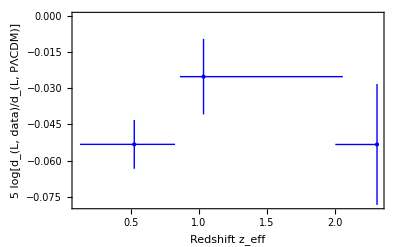

```mathematica
BAO1=ListPlot[Table[{finBao[[i,1]],finBao[[i,2]]},{i,Length[finBao]}],PlotRange->All,Frame->True,FrameLabel->{"Redshift z_eff","5 log[d_(L, data)/d_(L, PΛCDM)]"},IntervalMarkers->"Bars",IntervalMarkersStyle-><|"Color"->Blue|>,PlotStyle->{Blue,PointSize[Medium]},AxesOrigin->{First[logDMRatiosWithErrors][[1]],Automatic},Ticks->{Automatic,Automatic}]
```

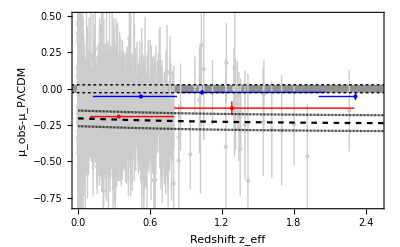

```mathematica
PlotTest=Show[pl1,pldmu,plRiessErr1,BAO1,Prolog->{HorizontalBand},Epilog->{{Dashing[0.005],Line[{{-30,sMplanck},{8,sMplanck}}],Line[{{-30,-sMplanck},{8,-sMplanck}}]}},PlotRange->{{0,2.5},{-0.8,0.5}}]
```

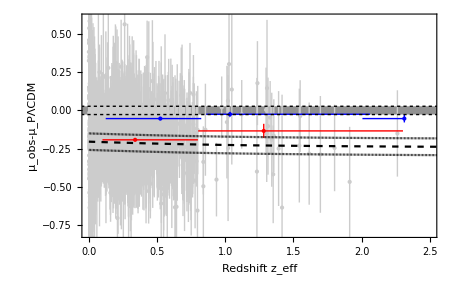

```mathematica
PlotTest1=Show[PlotTest,Frame->{{False,True},{True,True}},PlotRange->{{0,2.5},{-0.8,0.6}},ImageSize->455]
```

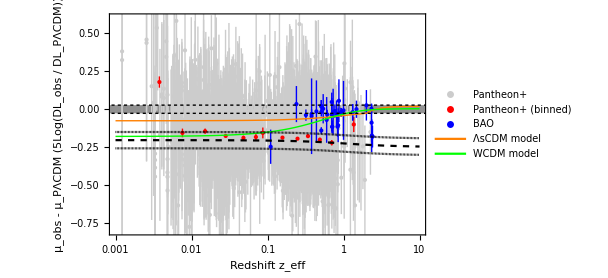

```mathematica
PlotTest2=Show[plfins1,Frame->{{True,True},{True,True}},PlotRange->{All,{-0.8,0.6}},ImageSize->450]
```

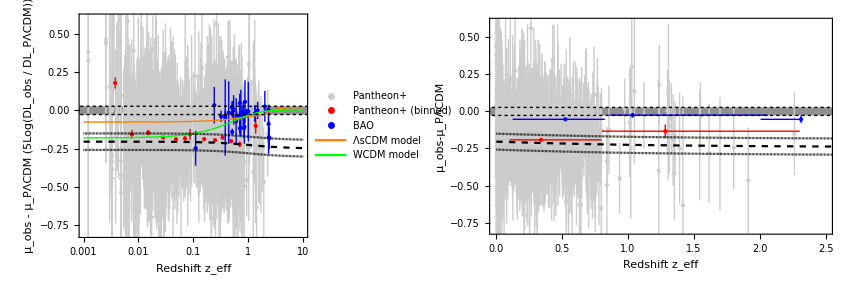

```mathematica
fig1=GraphicsGrid[{{PlotTest2,PlotTest1}},Spacings->-30,ImageSize->850,AspectRatio->Automatic]
```